```mathematica
n=10   (* velikost matrik *)
```

10

```mathematica
(* GENERIRANJE GOE, GUE, GSE *)
```

```mathematica
goe=RandomVariate[GaussianOrthogonalMatrixDistribution[n]];
```

```mathematica
gue=RandomVariate[GaussianUnitaryMatrixDistribution[n]];
```

```mathematica
gse=RandomVariate[GaussianSymplecticMatrixDistribution[n]];
```

```mathematica
(* GRAF GOSTOTE LASTNIH VREDNOSTI *)
```

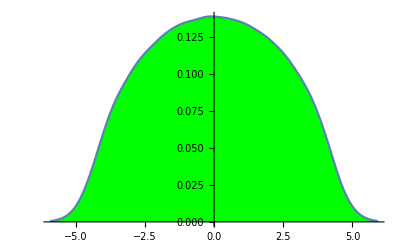
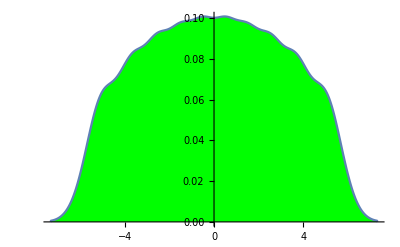
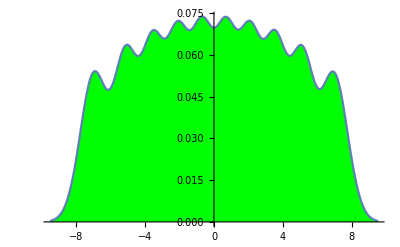

```mathematica
eigs=Flatten[RandomVariate[MatrixPropertyDistribution[Eigenvalues[x],x\[Distributed]#],10^5]]&/@{GaussianOrthogonalMatrixDistribution[n],GaussianUnitaryMatrixDistribution[n],GaussianSymplecticMatrixDistribution[n]};
Row[MapThread[SmoothHistogram[#1,"Scott",Frame->None,PlotLegends->Placed[#2,Above],Filling->Axis,FillingStyle->Green]&,{eigs,{Style["GOE",15],Style["GUE",15],Style["GSE",15]}}]]
```

```mathematica
(* LEVEL SPACING DISTRIBUTION *)
```

```mathematica
gaussiandists={GaussianOrthogonalMatrixDistribution[n],GaussianUnitaryMatrixDistribution[n],GaussianSymplecticMatrixDistribution[n]};
```

```mathematica
spacingdists=MatrixPropertyDistribution[{-1,1}.MinMax[Eigenvalues[x]],x\[Distributed]#]&/@gaussiandists;
```

```mathematica
gaps=Normalize[RandomVariate[#,10000],Mean]&/@spacingdists;
```

```mathematica
(* Analitic Level spacing distribution *)
WignerSurmisePDF[x_,β:1]:=Pi (x/2) Exp[-Pi (x/2)^2] (* GOE *)
WignerSurmisePDF[x_,β:2]:=2 (4 x/Pi)^2 Exp[(-4/Pi) x^2] (* GUE *)
WignerSurmisePDF[x_,β:4]:=(64/(9 Pi))^3 x^4 Exp[(-64/(9 Pi)) x^2] (* GSE *)
```

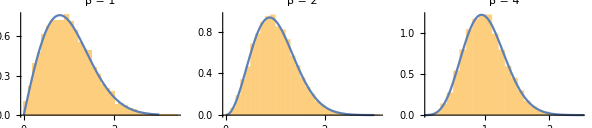

```mathematica
histogram=Histogram[#,{0.1},PDF]&/@gaps;
plot=Plot[WignerSurmisePDF[x,#],{x,0,3}]&/@{1,2,4};
GraphicsRow@MapThread[Show[#1,#2,ImageSize->180,PlotLabel->Row[{"β = ",#3}]]&,{histogram,plot,{1,2,4}}]
```